```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lehmann/results/nrqcd/2019-05-20/free

```mathematica
dt=0.2;
data = Import["mesoncorrelator_3s1.txt","Table"];
```

```mathematica
t=MapThread[#1&,{data[[2;;,1]]}];
c=MapThread[#1+I*#2&,{data[[2;;,2]],data[[2;;,3]]}];
retc=MapThread[{#1,#2}&,{data[[2;;,1]],data[[2;;,2]]}];
imtc=MapThread[{#1,#2}&,{data[[2;;,1]],data[[2;;,3]]}];
ftc[x_]:=Table[{w+I*w,0.5*dt*x[[1]]+0.5*dt*x[[-1]]*Exp[I*w*Length[x]*dt]+dt*Sum[x[[i]]*Exp[I*w*(i-1)*dt],{i,2,Length[x]-1}]},{w,-Pi/dt,+Pi/dt,2*Pi/dt/Length[x]}];
outtable[x_]:=Table[{Re[x[[i,1]]],2*Im[x[[i,2]]]},{i,1,Length[x]}];
ot=outtable[ftc[c]];
Export["spectrum_3s1.txt",ot,"Table"];
```

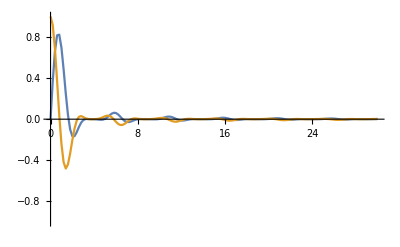

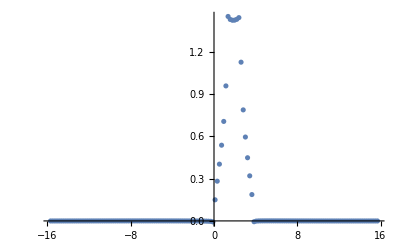

```mathematica
ListLinePlot[{retc,imtc},PlotRange->{All,{-1,+1}}]
ListPlot[Im[ftcor],PlotRange->All]
```